```mathematica
SetDirectory[NotebookDirectory[]];
```

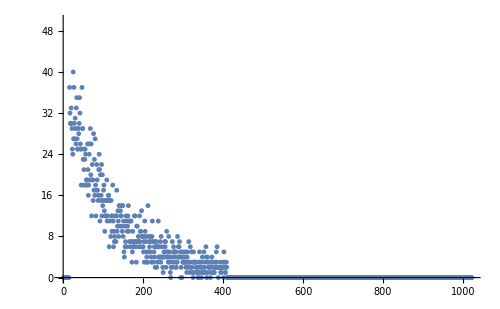
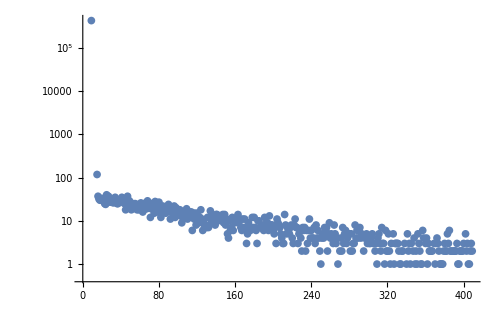

```mathematica
data = Drop[Flatten[Import["zerfallszeit.TKA", "Table"]], 2];
{ListPlot[data, PlotRange->{0, 50}, ImageSize->500], ListLogPlot[data, PlotRange->All, ImageSize->500]}
```

```mathematica
data[[9]] = 0;
```

```mathematica
fitdata = data[[;;400]];
fitdata = Drop[Table[{0.28 + 0.0189*c, fitdata[[c]]}, {c, 1, Length[fitdata]}], 14];
nlm = NonlinearModelFit[fitdata, A ⅇ^(-x/τ), {A, τ}, x]
nlm["ParameterTable"]
```

FittedModel[47.9847 ⅇ^(-0.499514 x)]

| Estimate | Standard Error | t-Statistic | P-Value
A | 47.9847 | 1.74599 | 27.4828 | 1.03493×10^-92
τ | 2.00195 | 0.0794594 | 25.1946 | 2.25347×10^-83

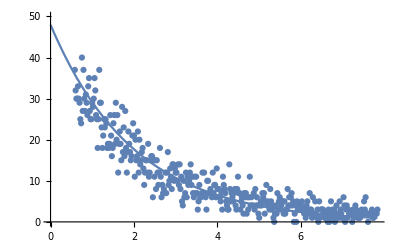

```mathematica
Show[Plot[Normal[nlm], {x, 0, 0.28+400*0.0189}, PlotRange->{0, 50}], ListPlot[fitdata]]
```